# Connecting to QPU Services

The Wolfram Quantum Framework lets you build, simulate and analyze quantum circuits symbolically and numerically. The same circuit object can also be sent to real quantum processing units (QPUs) hosted in the cloud. This tutorial covers the three pieces you need for that: OpenQASM, the portable text format that QPUs speak; the IBM Quantum platform; and Amazon Braket, which exposes several hardware vendors through a single service.

Everything in the OpenQASM section runs locally with no account. The hardware sections need credentials with the respective provider, and those cells are marked so you can read the tutorial without running them. For help, write to quantum@wolfram.com.

```mathematica
<< Wolfram`QuantumFramework`
```

## OpenQASM: the common language of QPUs

A quantum circuit built in the Wolfram Language is a symbolic object. To run it on hardware it has to be expressed in a format the device understands, and the de facto standard is OpenQASM. Both IBM and Amazon Braket accept OpenQASM, so it is the bridge between a QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol and the cloud.

Build a small reference circuit that we reuse throughout: a three-qubit GHZ state GHZ=1/(√2)(000+111), followed by a quantum Fourier transform and a measurement of all three qubits.

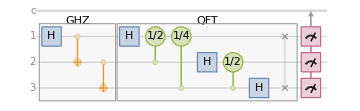

```mathematica
qc = QuantumCircuitOperator[{"GHZ", "Fourier"[3], {1, 2, 3}}];
qc["Diagram"]
```

QuantumQASMpaclet:Wolfram/QuantumFramework/ref/QuantumQASMWolfram/QuantumFramework Package Symbol is the single hub for OpenQASM. Called on a circuit with no extra arguments it emits OpenQASM 3.0 natively, in pure Wolfram Language with no external dependency, serializing the circuit exactly as built. Measurements become classical-bit assignments:

```mathematica
QuantumQASM[qc]
```

OPENQASM 3.0;
qubit[3] q;
bit[3] c;
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[1] q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 0.7853981633974483) q[2] q[0];
U(1.5707963267948966, 0., 3.141592653589793) q[1];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[2] q[1];
U(1.5707963267948966, 0., 3.141592653589793) q[2];
swap q[0] q[2];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];

The hub is also an importer: handing OpenQASM source (or a .qasm file) back to QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol reconstructs the circuit, again with no external dependency. The round trip recovers a circuit equal to the original:

```mathematica
QuantumCircuitOperator[QuantumQASM[qc]] == qc
```

True

OpenQASM 3.0 is the native and recommended target. For older toolchains that still require the legacy qelib1.inc gate set, pass "Version" -> 2 to emit OpenQASM 2.0. This path renders through Qiskit, so it needs the Python Qiskit stack configured:

```mathematica
QuantumQASM[qc, "Version" -> 2]
```

## IBM Quantum

### Connecting to the IBM Quantum Platform

Create an account at quantum.cloud.ibm.com. From the dashboard you need two things: an IAM API key (the long secret string shown once when you create the key, not the key's display name) and the instance CRN (a crn:v1:… string identifying your instance).

The API key is a secret and is stored in your encrypted system credential store. The CRN is read from a local symbol that the connection consults when it builds the request headers, so set both before connecting:

```mathematica
api = "XXX";
LocalSymbol["ibm_crn"] = "XXX";
```

Loading the Wolfram Quantum Framework registers the IBM Quantum Platform service automatically, so ServiceConnectpaclet:ref/ServiceConnect recognizes the "IBMQuantumPlatform" name directly:

```mathematica
ibm = ServiceConnect["IBMQuantumPlatform", "New", Authentication -> {"apikey" -> api}]
```

A connected service object lists the QPUs your account can reach through "Backends". Submitting and retrieving jobs is handled for you by IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol and the IBMJobpaclet:Wolfram/QuantumFramework/ref/IBMJobWolfram/QuantumFramework Package Symbol handle, shown below. List the available backends:

```mathematica
ibm["Backends"]
```

### Building and checking a circuit

Using the circuit qc from the previous section, plot its exact output distribution: the noiseless ground truth a QPU run approximates, and the reference we overlay with the hardware counts:

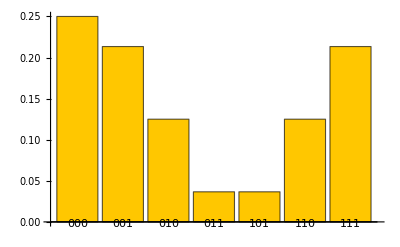

```mathematica
qc[]["ProbabilityPlot"]
```

Before spending QPU time, you can sample the circuit on a local noiseless simulator. QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol's "Qiskit" interface runs through a local Qiskit Aer simulator when no provider is given, returning a QuantumMeasurementpaclet:Wolfram/QuantumFramework/ref/QuantumMeasurementWolfram/QuantumFramework Package Symbol whose statistics converge to the exact distribution as the shot count grows (this needs the Python Qiskit stack):

```mathematica
qc["Qiskit"]["Shots" -> 4096]["ProbabilityPlot"]
```

### Running on hardware

With an active connection, IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol is the one call that runs a circuit on a QPU. It transpiles the circuit against the backend's own error-aware Target (per-instruction error and duration), submits it through the SamplerV2 primitive, and returns immediately with an asynchronous IBMJobpaclet:Wolfram/QuantumFramework/ref/IBMJobWolfram/QuantumFramework Package Symbol handle while the job sits in the queue. There is no manual OpenQASM, no raw request and no hex decoding of the classical register: the handle carries the per-bit to qubit map captured at transpile time, so results come back already in the Wolfram Language qubit order.

```mathematica
job = IBMJobSubmit[qc, "ibm_fez"]
```

The handle reports the job's status. Poll it while the job is queued, or pass "Wait" -> True to IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol to block until the job reaches a terminal status:

```mathematica
job["Status"]
```

Refresh the handle to pull a fresh snapshot from the service. Once the status is "Completed", applying the handle returns the measurement reconstructed from the hardware counts, in the Wolfram Language qubit order:

```mathematica
qpu = job["Refresh"][]
```

The same handle keeps every response IBM returns under "Raw" and exposes curated accessors on top, so the run's metadata is one query away. For example, the billed quantum runtime:

```mathematica
job["QuantumSeconds"]
```

### Comparing exact and hardware results

Putting the exact distribution next to the hardware run shows the structure surviving the device noise: the dominant 000, 001 and 111 outcomes and the near-zero 100 all come through, with the noise flattening the distribution. The hardware values below are qpu["Probabilities"] from a recorded ibm_fez run:

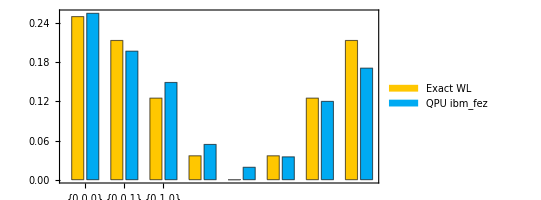

```mathematica
exact = N[Values[KeySort[FullSimplify /@ qc[]["Probabilities"]]]];
hardware = Values @ KeySort @ <|
    {0, 0, 0} -> 0.255, {0, 0, 1} -> 0.197, {0, 1, 0} -> 0.149, {0, 1, 1} -> 0.054,
    {1, 0, 0} -> 0.019, {1, 0, 1} -> 0.035, {1, 1, 0} -> 0.120, {1, 1, 1} -> 0.171|>;
BarChart[Transpose[{exact, hardware}],
    ChartLegends -> {"Exact WL", "QPU ibm_fez"},
    ChartLabels -> {Tuples[{0, 1}, 3], None},
    Frame -> True, AspectRatio -> 1/2]
```

The differences are not in the queries but in device noise: each shot passes through a deep transpiled circuit on superconducting hardware, and the noise varies from job to job.

## Amazon Braket

Amazon Braket is a quantum computing service on Amazon Web Services (AWS). Unlike IBM, which exposes its own superconducting devices, Braket fronts several vendors (IonQ, Rigetti, QuEra and others) and on-demand simulators through one API, which makes it convenient for comparing technologies side by side. The Wolfram Language reaches it through the standard AWS service connection.

### Connecting to AWS

Connect to AWS with your credentials (access key ID and secret access key); see the workflow Authenticate with Amazon Web Services for details on storing them:

```mathematica
aws = ServiceConnect["AWS", "New"]
```

Braket writes every task result to an S3 bucket, so you reach two AWS services through the connection: S3 for storage and Braket for the quantum tasks. If you do not have an S3 bucket yet, create one first:

```mathematica
s3 = ServiceExecute[aws, "GetService", {"Name" -> "S3"}];
braket = ServiceExecute[aws, "GetService", {"Name" -> "Braket"}];
```

```mathematica
braket["Requests"]["SearchDevices"]["GetDevice"]
```

{CancelJob,CancelQuantumTask,CreateJob,CreateQuantumTask,CreateSpendingLimit,DeleteSpendingLimit,GetDevice,GetJob,GetQuantumTask,ListTagsForResource,SearchDevices,SearchJobs,SearchQuantumTasks,SearchSpendingLimits,TagResource,UntagResource,UpdateSpendingLimit,RequestTemplate,ResponseTemplate}[SearchDevices][GetDevice]

### Finding devices

List the available devices, both simulators and QPUs:

```mathematica
devices = braket["Requests"]["SearchDevices", "Filters" -> {}]["Devices", All]
```

{CancelJob,CancelQuantumTask,CreateJob,CreateQuantumTask,CreateSpendingLimit,DeleteSpendingLimit,GetDevice,GetJob,GetQuantumTask,ListTagsForResource,SearchDevices,SearchJobs,SearchQuantumTasks,SearchSpendingLimits,TagResource,UntagResource,UpdateSpendingLimit,RequestTemplate,ResponseTemplate}[SearchDevices,Filters→{}][Devices,All]

```mathematica
devices[All, {"DeviceName", "DeviceType", "DeviceStatus"}]
```

ServiceExecute::aws-responseerror: The SearchDevices request failed with the following error from the server: "The request signature we calculated does not match the signature you provided. Check your AWS Secret Acc…0260618/us-east-1/braket/aws4_request
dc492338a6b7705daa2b4ecc14a29d19396ed391c567006fc3b705db1b6003e4'
"

Failure[…][Devices,All][All,{DeviceName,DeviceType,DeviceStatus}]

Select one on-demand simulator (Amazon's state-vector simulator SV1) and one QPU by their Amazon Resource Names (ARNs), decoding each device's capabilities from JSON:

```mathematica
sim = devices[
    SelectFirst[#DeviceArn == "arn:aws:braket:::device/quantum-simulator/amazon/sv1" &],
    MapAt[ImportString[#, "RawJSON"] &, "DeviceCapabilities"]];
qpu = devices[
    SelectFirst[StringContainsQ[#DeviceArn, "ionq"] &],
    MapAt[ImportString[#, "RawJSON"] &, "DeviceCapabilities"]];
```

### Preparing the circuit as OpenQASM

Build the circuit, then express it as OpenQASM for submission. Braket accepts OpenQASM, so the native QuantumQASMpaclet:Wolfram/QuantumFramework/ref/QuantumQASMWolfram/QuantumFramework Package Symbol output is a good way to inspect exactly what will be sent:

```mathematica
qc = QuantumCircuitOperator[{"GHZ", "Fourier"[3], {1, 2, 3}}];
QuantumQASM[qc]
```

OPENQASM 3.0;
qubit[3] q;
bit[3] c;
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[1] q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 0.7853981633974483) q[2] q[0];
U(1.5707963267948966, 0., 3.141592653589793) q[1];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[2] q[1];
U(1.5707963267948966, 0., 3.141592653589793) q[2];
swap q[0] q[2];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];

For submission to a specific Braket backend it is safest to render the device dialect of OpenQASM, which maps the circuit onto that vendor's supported gate set. Passing "Provider" -> "AWSBraket" to the Qiskit interface does this conversion (it needs the Python Qiskit and Braket providers configured):

```mathematica
qasm = qc["Qiskit"]["QASM", "Provider" -> "AWSBraket"];
```

### Submitting a quantum task

A Braket job is a "quantum task". Submit the OpenQASM as the task action, naming the device ARN, the destination S3 bucket and the number of shots. Run it once on the simulator:

```mathematica
taskSV1 = braket["CreateQuantumTask",
    "DeviceArn" -> sim["DeviceArn"],
    "Shots" -> 100,
    "Action" -> <|braketSchemaHeader -> <|name -> "braket.ir.openqasm.program", version -> "1"|>, source -> qasm|>,
    "OutputS3Bucket" -> "amazon-braket-my-bucket", "OutputS3KeyPrefix" -> "tasks",
    "RequestRegion" -> "us-east-1"]
```

The same call against the QPU ARN queues a hardware run:

```mathematica
taskIonQ = braket["CreateQuantumTask",
    "DeviceArn" -> qpu["DeviceArn"],
    "Shots" -> 100,
    "Action" -> <|braketSchemaHeader -> <|name -> "braket.ir.openqasm.program", version -> "1"|>, source -> qasm|>,
    "OutputS3Bucket" -> "amazon-braket-my-bucket", "OutputS3KeyPrefix" -> "tasks",
    "RequestRegion" -> "us-east-1"]
```

### Checking status and fetching results

Query a task by its ARN. The simulator usually completes in seconds; a QPU task may sit QUEUED until the device is available:

```mathematica
braket["GetQuantumTask", "QuantumTaskArn" -> taskSV1["quantumTaskArn"], "RequestRegion" -> "us-east-1"]["status"]
```

The result is written to S3. Locate its directory, then read results.json from the bucket:

```mathematica
outputPath = braket["GetQuantumTask",
    "QuantumTaskArn" -> taskSV1["quantumTaskArn"], "RequestRegion" -> "us-east-1"]["outputS3Directory"];
results = ImportByteArray[
    s3["GetObject", "Bucket" -> "amazon-braket-my-bucket",
        "Key" -> FileNameJoin[{outputPath, "results.json"}], "RequestRegion" -> "us-east-1"]["Body"],
    "RawJSON"];
```

The exact shape depends on the device: SV1 returns per-shot readouts under "measurements", while IonQ returns aggregated "measurementProbabilities". Either way you reduce to a probability over the eight basis states.

### Comparing exact and simulator results

SV1 is a noiseless state-vector simulator, so its finite-shot output is a sample from the exact distribution, exactly what QuantumMeasurementpaclet:Wolfram/QuantumFramework/ref/QuantumMeasurementWolfram/QuantumFramework Package Symbol's own sampler produces. Comparing the exact probabilities with a 100-shot sample shows the sampling spread you should expect before any device noise enters:

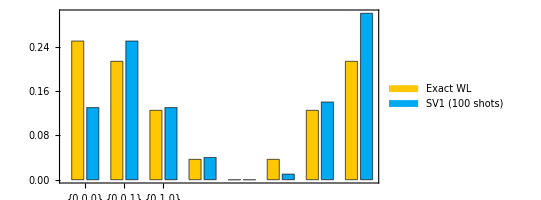

```mathematica
qc = QuantumCircuitOperator[{"GHZ", "Fourier"[3], {1, 2, 3}}];
exact = N[qc[]["ProbabilitiesList"]];
ordered = Keys[KeySort[qc[]["Probabilities"]]];
SeedRandom[42];
counts = Counts[qc[]["SimulatedMeasurement", 100]];
sv1 = N[Lookup[counts, ordered, 0]]/100;
BarChart[Transpose[{exact, sv1}],
    ChartLegends -> {"Exact WL", "SV1 (100 shots)"},
    ChartLabels -> {Tuples[{0, 1}, 3], None},
    Frame -> True, AspectRatio -> 1/2]
```

On a real QPU the same overlay would show the additional device noise, just as the IBM run did above. Running the IonQ task and reading back its "measurementProbabilities" gives the third bar to add to this chart.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

GettingStartedpaclet:Wolfram/QuantumFramework/tutorial/GettingStarted ▪ Tutorialpaclet:Wolfram/QuantumFramework/tutorial/Tutorial

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/QPUServiceConnect

### Keywords

OpenQASM

QPU

IBM Quantum

Amazon Braket

AWS

Qiskit

ServiceConnect

quantum hardware

sampler